```mathematica
StreamPlot[{y - x, x^2}, {x, -10, 10}, {y, -10, 10}]
```

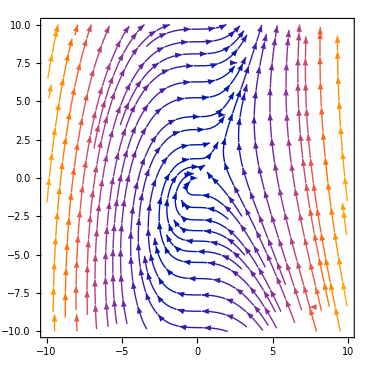

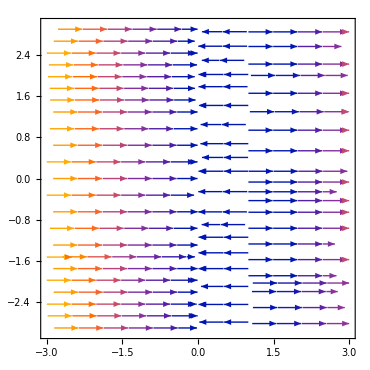

```mathematica
StreamPlot[{a*r + r^2, 0} /. {a -> -1} , {r, -3, 3}, {θ, -3, 3}]
```

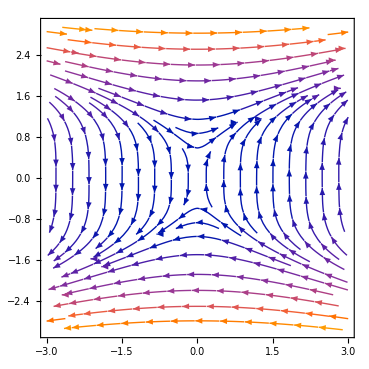

```mathematica
StreamPlot[{y^3, x}, {x, -3, 3}, {y, -3, 3}]
```

```mathematica
Clear["Global`*"]
n = .;
f[x_, y_] := (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
g[x_, y_]:=(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
ϕ[x_,y_] := ArcTan[g[x,y]/f[x,y]];
I = (Integrate[D[ϕ[1, y], y],{y, -1, 1}] + Integrate[D[ϕ[x, -1], x],{x, -1, 1}] + Integrate[D[ϕ[-1, y], y],{y, 1, -1}] + Integrate[D[ϕ[x, 1], x],{x, 1, -1}]) / (2*π)
```

n